## Feshbach resonance parameter from fitting Rb-Na molecule binding energy by coupled square well model

Authors: Zhichao Guo<guozc12@gmail.com>, Fan Jia <fjia@phy.cuhk.edu.hk>

Version: 2.0
Date: 2020.01.09
Due to failure fitting of the Feshbach resonance point, we try to find the problem in the theoretical model. By following the derivation of coupled square well model, we understand that the main idea of it is to expand the coupled one to the first order of the non-coupling solution. however, this need several approximation which can not be satisfied in our case: a_bg is not much larger than ā which make k_m not a small value, then will be conflict to the derivation above. Moreover, taking the point of view from the fitting model, if a_bg!>>ā, the fitting model will degenerate to a simple formula where a_bg and Δ couple to each other, rendering failure of fitting.

Version:1.0
Date: 2019.10.25
Following the model in PRA79,013622(A.D.Lange et al "Determination of  atomic scattering lengths from measurements of molecular binding energies near Feshbach resonances"), we re-fit Rb-Na Feshbach resonance parameters for both 347G and 478G at same time. Due to no analytical solution for fitting function, we minimize the summation of residue to get the solution. Fitting data is compared with independent fitting for each resonance. The fitting still failure, which generate gap of residues when adding 478G into 347G fitting.

### Global Function

```mathematica
ClearAll["Global`*"];
```

```mathematica
Cons={
h->6.62606896*10^-34,
ℏ->h/(2π),
c->299792458,
AMU->1.6605402*10^-27,
α->e^2/(4π Subscript[ϵ, 0] ℏ c),
mp->1.67262174797*10^-27,
me->9.10938215*10^-31,
a0->(4π Subscript[ϵ, 0] ℏ^2)/(me e^2),
hartree->4.35974417 10^-18,
E0->(e^4 me)/(32 π^2 ℏ^2 Subscript[ϵ, 0]^2),
e->1.602176487*10^-19,
Subscript[ϵ, 0]->8.854187817*10^-12,
Subscript[μ, 0]->4π*10^-7,
μN->5.050783424*10^-27,
Subscript[μ, B]->9.27400915*10^-24,
kb->1.380658*10^-23,
grav->9.8,
Subscript[g, e]->2,
Z->1
};
```

### Rb Na constants

##### Rb Na mass

```mathematica
mRb=86.909187*AMU;(*Rb mass in atomic mass unit*)
mNa=22.989767*AMU;(*Na mass in atomic mass unit*)
mr=(mRb*mNa)/(mRb+mNa);(*Na mass in atomic mass unit*)
```

##### vdW parameters

```mathematica
A0=10^-10;
C6=(1.29463596372576691*10^7)/10^-2*A0^6*h*c//.Cons;(*Data from https://iopscience.iop.org/article/10.1088/1367-2630/17/3/035003/pdf*)
RvdW=1/2(2mr C6/ℏ^2)^(1/4)//.Cons;(*about 3nm*)
EvdW=ℏ^2/(2mr RvdW^2)//.Cons; (*aout 30MHz*)
abar=4π Gamma[1/4]^-2 RvdW//.Cons; (*about 3nm, about 55.2*a0*)
```

### A#0 theory of Feshbach resonance and binding energy

-Graphics-

Figure from PRA79,013622

##### For scattering state above threshold, we can have formula for scattering length

Now, we start to derive the connection formula from the original Schrodinger equation

(ℏ^2/(2 m_r)+V̂) |ϕ> = E|ϕ>

potential is

V̂=Piecewise[{{(-V_c | ℏ Ω
ℏ Ω | -V_e), R<ā}, {(∞ | 0
0 | 0), R>ā}}]

wavefunction can be written as

|ϕ>=Piecewise[{{C_1(Sin[q_+R]/R(Cos[θ]|e>+Sin[θ]|c>)+(A Sin[q_-R])/R(-Sin[θ]|e>+Cos[θ]|c>)), R<ā}, {C_2 Sin[k R+η]/R|e>, R>ā}}]

where

(ℏ^2 q_±^2)/(2 m_r)=E+1/2(V_e+V_c)±1/2(V_e-V_c)1/Cos[2θ]
Tan[2θ]=(2ℏ Ω)/(V_e-V_c)

i.e.

|ϕ>=Piecewise[{{(C_1(Sin[q_+R]Cos[θ])/R-C_1 A(Sin[q_-R]Sin[θ])/R)|e>+(C_1(Sin[q_+R]Sin[θ])/R+C_1 A(Sin[q_-R]Cos[θ])/R)|c>), R<ā}, {C_2 Sin[k R+η]/R|e>, R>ā}}]

when we take

R=ā

we have continue condition (notice that |c> state only require wave function continue at R=ā, but not necessary for gradient), i.e.

(Sin[q_+ā]Sin[θ])/(ā)+A(Sin[q_-ā]Cos[θ])/(ā)=0
C_1(Sin[q_+ā]Cos[θ])/(ā)-C_1 A(Sin[q_-ā]Sin[θ])/(ā)=C_2 Sin[k ā+η]/(ā)
C_1(q_+ā Cos[q_+ā]-Sin[q_+ā])/(ā)^2 Cos[θ]-C_1 A(q_-ā Cos[q_-ā]-Sin[q_-ā])/(ā)^2 Sin[θ]=C_2(k Cos[k ā+η]ā-Sin[k ā+η])/(ā)^2

i.e.

Sin[q_+ā]Sin[θ]=-A Sin[q_-ā]Cos[θ]
Sin[q_+ā]Cos[θ]-A Sin[q_-ā]Sin[θ]=C_2/C_1 Sin[k ā+η]
(q_+ā Cos[q_+ā]-Sin[q_+ā])Cos[θ]-A(q_-ā Cos[q_-ā]-Sin[q_-ā])Sin[θ]=C_2/C_1(k Cos[k ā+η]ā-Sin[k ā+η])

i.e.

Sin[q_+ā]Sin[θ]=-A Sin[q_-ā]Cos[θ]
(q_+ā Cos[q_+ā]Cos[θ]-A q_-ā Cos[q_-ā]Sin[θ])/(Sin[q_+ā]Cos[θ]-A Sin[q_-ā]Sin[θ])=(k ā)/Tan[k ā+η]

i.e.

(Sin[q_+ā]Sin[θ])/(Sin[q_-ā]Cos[θ])=-A 
(q_+ā Cos[q_+ā]Cos[θ]+(Sin[q_+ā]Sin[θ])/(Sin[q_-ā]Cos[θ]) q_-ā Cos[q_-ā]Sin[θ])/(Sin[q_+ā]Cos[θ]+(Sin[q_+ā]Sin[θ])/(Sin[q_-ā]Cos[θ]) Sin[q_-ā]Sin[θ])=(k ā)/Tan[k ā+η]

i.e. (**)

(q_+)/Tan[q_+ā]Cos[θ]^2+(q_-)/Tan[q_-ā] Sin[θ]^2=k/Tan[k ā+η]

When Ω→0, coupling is approaching zero

i.e.

(ℏ^2 q_±^2)/(2 m_r)=E+1/2(V_e+V_c)±1/2(V_e-V_c)(1+2 θ^2)
Tan[2θ]=(2ℏ Ω)/(V_e-V_c)=2θ

i.e.

(ℏ^2 q_+^2)/(2 m_r)=E+V_e+(V_e-V_c)θ^2
(ℏ^2 q_-^2)/(2 m_r)=E+V_c-(V_e-V_c)θ^2
θ=(ℏ Ω)/(V_e-V_c)

consider non-coupling limit (θ=0), we have (***)

(q_+)/Tan[q_+ā]=k/Tan[k ā+η_bg]
Sin[q_(-,0)ā]=0
where q_(-,0)=ℏ^-1 √(2m_r(E_c+V_c))

put them into (**) formula, we have

Cot[k ā+η_bg]Cos[θ]^2+(q_-/k)/Tan[q_-ā] Sin[θ]^2=Cot[k ā+η]

take θ as a small number

Cot[k ā+η_bg]+(Tan[q_-ā]/(q_-ā))^-1 θ^2/(k ā)=Cot[k ā+η]

Then, expand Tan[q_-ā]/(q_-ā) around (***), we have

Tan[q_-ā]/(q_-ā)=Tan[q_(-,0)ā]/(q_(-,0)ā)+(q_(-,0)ā Sec[q_(-,0)ā]^2-Tan[q_(-,0)ā])/(q_(-,0)ā)^2 δ(ā q_-)
=(δ(ā q_-))/(q_(-,0)ā)=(δ(q_-))/(q_(-,0))

where

(ℏ^2 q_-^2)/(2 m_r)=(ℏ^2 q_(-,0)^2)/(2 m_r)+(E-E_c)-(V_e-V_c)θ^2=(V_c+E_c)+(E-E_c)-(V_e-V_c)θ^2

i.e.

(δ(q_-))/(q_(-,0))=1/2((E-E_c)-(V_e-V_c)θ^2)/(V_c+E_c)

because E<<E_c<<V_c

Tan[q_-ā]/(q_-ā)=-E_c/(2 V_c)

then, we have

Cot[k ā+η_bg]-(2 V_c)/E_c θ^2/(k ā)=Cot[k ā+η]

replace η by scattering length a=-lim_(k→0) (k Cot[η])^-1, we have

(2 V_c)/E_c θ^2/(k ā)=Cot[k ā+η_bg]-Cot[k ā+η]=(Cot[k ā]Cot[η_bg]-1)/(Cot[k ā]+Cot[η_bg])-(Cot[k ā]Cot[η]-1)/(Cot[k ā]+Cot[η])
=(Cot[η_bg]-k ā)/(1+k ā Cot[η_bg])-(Cot[η]-k ā)/(1+k ā Cot[η])=(1/(k a_bg)-k ā)/(1- ā/a_bg)-(1/(k a)-k ā)/(1-ā/a)=(1/k+a_bg k ā)/(a_bg- ā)-(1/k+a k ā)/(a- ā)

i.e.

(2 V_c)/(E_c ā)θ^2=(1+a_bg/(ā)(k ā)^2)/(a_bg- ā)-(1+a/(ā)(k ā)^2)/(a- ā)=1/(-a_bg+ ā)-1/(-a+ ā)

i.e.

1/(a-ā)=1/(a_bg-ā)+(Γ/2)/(ā E_c)

where Γ is Feshbach coupling strength
ā is mean scattering length, which has been calculated from vdW parameters
a_bg is background scattering length
E_c=δμ(B-B_c) is the bound state energy of pure closed channel
and a is scattering length for scattering state, which can be noted as

a=a_bg(1-Δ/(B-B_0))

where B_0 and Δ are given by

Δ=(a_bg-ā)^2/(a_bg ā)Γ/(2δμ)

B_0=B_c-a_bg/(a_bg-ā)Δ

##### For bound molecular state below threshold, we can have formula for binding energy

Following the scattering case, we try to derive the bound case: For a bound state with binding energy

E_b=(ℏ^2 k_m^2)/(2 m_r)

Solving Schrodinger equation, we have wave function

|ϕ>=Piecewise[{{C_1(Sin[(q̄)_+R]/R(Cos[θ]|e>+Sin[θ]|c>)+(A Sin[(q̄)_-R])/R(-Sin[θ]|e>+Cos[θ]|c>)), R<ā}, {C_2 Exp[-k_mR]/R|e>, R>ā}}]

where

(q̄)_±=(q_±^2-k^2-k_m^2)^(1/2)

i.e.

(ℏ^2(q̄)_-^2)/(2 m_r)=(ℏ^2 q_-^2)/(2 m_r)-E-E_b=(ℏ^2 q_(-,0)^2)/(2 m_r)+(E-E_c)-(V_e-V_c)θ^2-E-E_b=(ℏ^2 q_(-,0)^2)/(2 m_r)-(E_b+E_c)-(V_e-V_c)θ^2

Then, we have

|ϕ>=Piecewise[{{(C_1(Sin[(q̄)_+R]Cos[θ])/R-C_1 A(Sin[(q̄)_-R]Sin[θ])/R)|e>+(C_1(Sin[(q̄)_+R]Sin[θ])/R+C_1 A(Sin[(q̄)_-R]Cos[θ])/R)|c>), R<ā}, {C_2 Exp[-k_mR]/R|e>, R>ā}}]

Then, we take R=ā, apply the continue condition

(Sin[(q̄)_+ā]Sin[θ])/(ā)+A(Sin[(q̄)_-ā]Cos[θ])/(ā)=0
C_1(Sin[(q̄)_+ā]Cos[θ])/(ā)-C_1 A(Sin[(q̄)_-ā]Sin[θ])/(ā)=C_2 Exp[-k_m ā]/(ā)
C_1((q̄)_+ā Cos[(q̄)_+ā]-Sin[(q̄)_+ā])/(ā)^2 Cos[θ]-C_1 A((q̄)_-ā Cos[(q̄)_-ā]-Sin[(q̄)_-ā])/(ā)^2 Sin[θ]=C_2(-k_m Exp[-k_mR]ā-Exp[-k_mR])/(ā)^2

i.e.

(Sin[(q̄)_+ā]Sin[θ])/(Sin[(q̄)_-ā]Cos[θ])=-A 
(Sin[(q̄)_+ā]Cos[θ]-A Sin[(q̄)_-ā]Sin[θ])/Exp[-k_m ā]=C_2/C_1
((q̄)_+ā Cos[(q̄)_+ā]-Sin[(q̄)_+ā])Cos[θ]-A((q̄)_-ā Cos[(q̄)_-ā]-Sin[(q̄)_-ā])Sin[θ]=C_2/C_1(-k_m Exp[-k_m ā]ā-Exp[-k_m ā])

i.e.

(((q̄)_+ā Cos[(q̄)_+ā]-Sin[(q̄)_+ā])Cos[θ]+(Sin[(q̄)_+ā]Sin[θ])/(Sin[(q̄)_-ā]Cos[θ])((q̄)_-ā Cos[(q̄)_-ā]-Sin[(q̄)_-ā])Sin[θ])/(Sin[(q̄)_+ā]Cos[θ]+(Sin[(q̄)_+ā]Sin[θ])/(Sin[(q̄)_-ā]Cos[θ]) Sin[(q̄)_-ā]Sin[θ])=(-k_m Exp[-k_m ā]ā-Exp[-k_m ā])/Exp[-k_m ā]

i.e.

(Tan[(q̄)_+ā]/((q̄)_+ā))^-1 Cos[θ]^2+(Tan[(q̄)_-ā]/((q̄)_-ā))^-1 Sin[θ]^2=-k_m ā

for small coupling, we have can take linear approx of θ. meanwhile, due to low-energy scattering and small binding energy approximation, we can take (q̄)_+ as small change of q_+

(q̄)_+=q_±(1-(k^2+k_m^2)/(2 q_+^2))=q_+-(k^2+k_m^2)/(2 q_+)

we have for term containing (q̄)_+

Tan[(q̄)_+ā]/((q̄)_+ā)=Tan[q_+ā]/(q_+ā)-(q_+ā Sec[q_+ā]^2-Tan[q_+ā])/(q_+ā)(k^2+k_m^2)/(2 q_+^2)
=Tan[q_+ā]/(q_+ā)(1+(k^2+k_m^2)/(2 q_+^2))-Sec[q_+ā]^2(k^2+k_m^2)/(2 q_+^2)
=Tan[q_+ā]/(q_+ā)(1+(k^2+k_m^2)/(2 q_+^2))-(1+Tan[q_+ā]^2)(k^2+k_m^2)/(2 q_+^2)
=Tan[q_+ā]/(q_+ā)(1+(k^2+k_m^2)/(2 q_+^2))-(k^2+k_m^2)/(2 q_+^2)-(Tan[q_+ā]/(q_+ā))^2(k^2+k_m^2)/2(ā)^2
∼Tan[q_+ā]/(q_+ā)-(Tan[q_+ā]/(q_+ā))^2(k^2+k_m^2)/2(ā)^2∼Tan[q_+ā]/(q_+ā)-(Tan[q_+ā]/(q_+ā))^2 k_m^2/2(ā)^2

for (q̄)_-, same as we derive in the scattering part, we have

Tan[(q̄)_-ā]/((q̄)_-ā)=Tan[q_(-,0)ā]/(q_(-,0)ā)+(q_(-,0)ā Sec[q_(-,0)ā]^2-Tan[q_(-,0)ā])/(q_(-,0)ā)^2 δ(ā(q̄)_-)=(δ((q̄)_-))/(q_(-,0))
=-1/2((E_b+E_c)+(V_e-V_c)θ^2)/(V_c+E_c)∼-1/2(E_b+E_c)/V_c

Finally, we have

(Tan[q_+ā]/(q_+ā)-(Tan[q_+ā]/(q_+ā))^2 k_m^2/2(ā)^2)^-1 Cos[θ]^2+(-1/2(E_b+E_c)/V_c)^-1 Sin[θ]^2=-k_m ā

i.e.

(q_+ā)/Tan[q_+ā]+(k_m^2(ā)^2)/2-(2 V_c θ^2)/(E_b+E_c)=-k_m ā

i.e.

k_m+(k_m^2 ā)/2=(2 V_c θ^2)/(ā(E_b+E_c))-(q_+)/Tan[q_+ā]

i.e.

k_m+(k_m^2 ā)/2=(2 V_c θ^2)/(ā(E_b+E_c))-k/Tan[k ā+η_bg]=(2 V_c θ^2)/(ā(E_b+E_c))-k/Tan[k ā+η_bg]

√((2 m_r E_b)/ℏ^2)+(m_r E_b ā)/ℏ^2=1/(a_bg-ā)+(Γ/2)/(ā(E_b+E_c))

where Γ is Feshbach coupling strength
ā is mean scattering length, which has been calculated from vdW parameters
a_bg is background scattering length
E_b and E_c are binding energy of bound molecule and bound state energy of pure closed channel, which can be noted as

E_c=δμ(B-B_c)

##### Note!!!

Above derivation implies several approximation, which need to be clarified here:

Zeros, we need the bare bound state in close channel to be a level with high index, which means there are many states supported be the close channel and we only consider the one very near the entrance threshold, i.e. V_c, V_e>>E_vdw

First, we take coupling as a small value, which means θ<<1

Second, we need approximation about V_c, V_e and E_c: E_c<<V_c

Third, we need E(k) and E_b(k_m) to be small relative to E_vdw, which allow as to expand q_±

Fourth, we need a_bg>>ā, which make sure that k_m keep small value.

Thus, for our Rb and Na case, the last condition not satisfied, lead to bad fitting.

In the following fitting approach, we will recall this failure in another explanation.

### A#1. Fitting for 347G resonance independently

##### Fitting model

Combining above formula, we have

B=B_c+(√((2 mr E_b)/ℏ^2)+(m_r E_b ā)/ℏ^2-1/(a_bg-ā))^-1 Γ/(2δμ)-E_b/δμ

replacing Γ by other parameters, we have

B=B_c+(√((2 mr E_b)/ℏ^2)+(m_r E_b ā)/ℏ^2-1/(a_bg-ā))^-1(Δ a_bg)/(a_bg-ā)^2-E_b/δμ

Then fitting parameter is δμ, a_bg, B_c and Δ

```mathematica
modelA1=(B0+(abg Δ)/(abg-abar/a0)+(√((4π mr Eb)/ℏ)a0+(mr Eb abar a0)/ℏ-1/(abg-abar/a0))^-1(Δ abg)/(abg-abar/a0)^2-Eb/δμ)//.Cons//FullSimplify
```

B0+(abg (-55.2149+abg+1/(-1./(-55.2149+abg)+3.17392×10^-6 √Eb+4.42628×10^-11 Eb)) Δ)/(-55.2149+abg)^2-Eb/δμ

##### Note!!!

Recall the problem in our Rb-Na case: if abg is not much larger than ā=55.2 a_0, we will have

α=+3.17392×10^-6 √Eb+4.42628×10^-11 Eb ∼10^-3
β=-1./(-55.2149+abg)∼10^-1
i.e. α<<β

thus, we cannot directly take β as small value and make approximation to the above formula, i.e.

B0-Eb/δμ-(abg Δ 3.17392×10^-6)√Eb

where abg and Δ couple to each other. Thus we cannot extract effective information about them.
Which means the method is failure.

##### Data

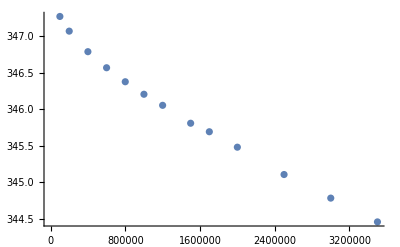

```mathematica
DataA1=Import[FileNameJoin[{NotebookDirectory[],"347Gdata.txt"}],"Data"];
DataA1=DataA1[[All,1;;2]];
DataA1[[All,1]]=-DataA1[[All,1]]*10^6//.Cons;
ListPlot[DataA1]
```

##### Fitting...

B0+(3.65646+1/(-0.273488+0.0000180421 √Eb+2.51611×10^-10 Eb)) Δ-Eb/δμ

-73.3604

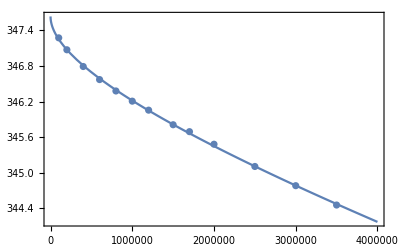

| Estimate | Standard Error | t-Statistic | P-Value
Δ | 4.64996 | 0.236983 | 19.6215 | 2.58664×10^-9
δμ | 5.05141×10^6 | 786474. | 6.42286 | 0.0000760681
B0 | 347.634 | 0.0283838 | 12247.6 | 3.24028×10^-37

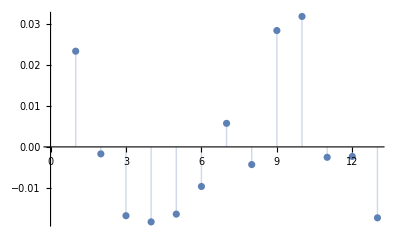

```mathematica
abg0=76;
modelA1=(B0+(abg Δ)/(abg-abar/a0)+(√((4π mr Eb)/ℏ)a0+(mr Eb abar a0)/ℏ-1/(abg-abar/a0))^-1(Δ abg)/(abg-abar/a0)^2-Eb/δμ)/.abg->abg0//.Cons//FullSimplify
nlm=NonlinearModelFit[DataA1,{modelA1},{{Δ,5},{δμ,1000000},{B0,347.53}},Eb];
a350 =abg*(1-Δ/(350-B0))/.abg->abg0/.nlm["BestFitParameters"]
Show[ListPlot[DataA1],Plot[nlm[x],{x,0,4*10^6//.Cons}],Frame->True,PlotRange->All]
nlm["ParameterTable"]
ListPlot[nlm["FitResiduals"],Filling->Axis]
```

### A#2. Fitting for 478G resonance independently

##### Fitting model

Same as ModelA1

##### Data

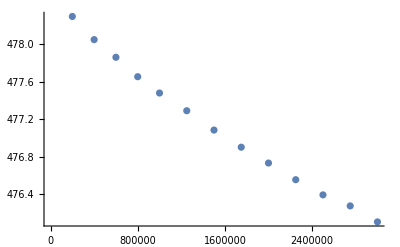

```mathematica
DataA1=Import["D:\\Dropbox\\@JClubGroupMeeting\\GM191026\\478Gdata.txt","Data"];
DataA1=DataA1[[All,1;;2]];
DataA1[[All,1]]=-DataA1[[All,1]]*10^6//.Cons;
ListPlot[DataA1]
```

##### Fitting...

FittedModel[478.847+5.02206 (5.77839+1/(-«19»+«21» «1»))-2.60249×10^-7 Eb]

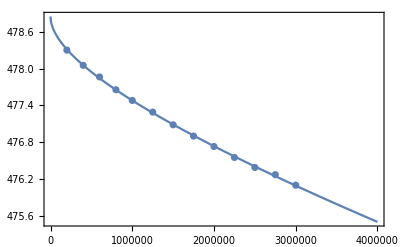

| Estimate | Standard Error | t-Statistic | P-Value
Δ | 5.02206 | 0.298767 | 16.8093 | 1.1651×10^-8
δμ | 3.84247×10^6 | 449879. | 8.54112 | 6.60764×10^-6
B0 | 478.847 | 0.0328717 | 14567.1 | 5.71947×10^-38

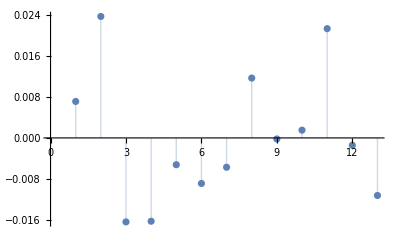

```mathematica
nlm=NonlinearModelFit[DataA1,{modelA1},{{Δ,5},{δμ,5000000},{B0,478}},Eb]
Show[ListPlot[DataA1],Plot[nlm[x],{x,0,4*10^6//.Cons}],Frame->True,PlotRange->All]
nlm["ParameterTable"]
ListPlot[nlm["FitResiduals"],Filling->Axis]
```

### B. Fitting for both resonance

As described in PRA79,013622, for multipole overlapping Feshbach resonance, we need to consider the effect of 478G resonance on 347G resonance.

##### For bound molecule state

√((2mr E_b)/ℏ^2)=1/(a_bg-ā)+(Γ_1/2)/(ā(E_b+E_c1))+(Γ_2/2)/(ā(E_b+E_c2))

where

E_c1=δμ_1(B-B_c1)

E_c2=δμ_2(B-B_c2)

##### For scattering state

1/(a-ā)=1/(a_bg-ā)+1/(ā)((Γ_1/2)/E_c1+(Γ_2/2)/E_c2)

a=a_bg(1-Δ_1/(B-B_01))(1-Δ_2/(B-B_02))

where

Δ_1=(a_bg-ā)^2/(a_bg ā)Γ_1/(2 δμ_1), Δ_2=(a_bg-ā)^2/(a_bg ā)Γ_2/(2 δμ_2)

B_01=B_c1-a_bg/(a_bg-ā)Δ_1, B_02=B_c2-a_bg/(a_bg-ā)Δ_2

##### Fitting model

Combining all above formula, we have

ā √((2mr E_b)/ℏ^2)-(ā)/(a_bg-ā)=(Γ_1/2)/(E_b+δμ_1(B-B_c1))+(Γ_2/2)/(E_b+δμ_2(B-B_c2))

(a_bg-ā)^2/a_bg(√((2mr E_b)/ℏ^2)-1/(a_bg-ā))=Δ_1/(E_b/δμ_1+B-B_01-a_bg/(a_bg-ā)Δ_1)+Δ_2/(E_b/δμ_2+B-B_02-a_bg/(a_bg-ā)Δ_2)

(a_bg-ā)/a_bg(√((2mr E_b)/ℏ^2)-1/(a_bg-ā))=Δ_1/((E_b/δμ_1+B-B_01)(a_bg-ā)-a_bg Δ_1)+Δ_2/((E_b/δμ_2+B-B_02)(a_bg-ā)-a_bg Δ_2)

(a_bg-ā/a0)/a_bg(a0 √((4π mr E_b)/ℏ)-1/(a_bg-ā/a0))=Δ_1/((E_b/δμ_1+B-B_01)(a_bg-ā/a0)-a_bg Δ_1)+Δ_2/((E_b/δμ_2+B-B_02)(a_bg-ā/a0)-a_bg Δ_2)

```mathematica
Res[Eb_,B_]:=((abg-abar/a0)/abg(a0 √((4π mr Eb*10^6)/ℏ)-1/(abg-abar/a0))-Δ1/((Eb*10^6/δμ1+B-B01)(abg-abar/a0)-abg Δ1)-Δ2/((Eb*10^6/δμ2+B-B02)(abg-abar/a0)-abg Δ2))^2//.Cons
```

##### Data

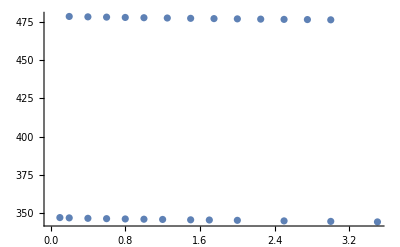

```mathematica
DataB=Import["D:\\Dropbox\\@JClubGroupMeeting\\GM191026\\347-478Gdata.txt","Data"];
DataB=DataB[[All,1;;2]];
DataB[[All,1]]=-DataB[[All,1]]//.Cons;
ListPlot[DataB]
```

##### Fitting...

```mathematica
res=Total[Res@@@DataB];
```

{9.36786×10^-8,{abg→89.9586,δμ1→2.77888×10^6,δμ2→3.86707×10^6,Δ1→2.18421,Δ2→3.4368,B01→347.774,B02→478.378}}

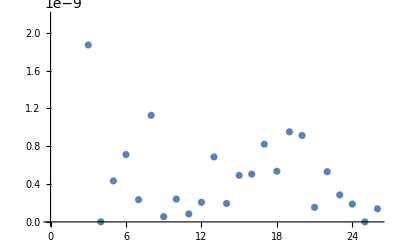

```mathematica
fit=FindMinimum[{res,348>B01>347&&479>B02>478&&10^4<δμ1<10^7&&10^4<δμ2<10^7&&150>abg>0&&0<Δ1<10&&0<Δ2<10},{{abg,66.77},{δμ1,3.7000179798241826*^6},{δμ2,3.8424676391519117*^6},{Δ1,10},{Δ2,5.02},{B01,347.635},{B02,478.8466750372356}}]
ListPlot@First[Res@@@DataB/.{Last@fit},PlotRange->All]
```

```mathematica
Manipulate[ListPlot[Res@@@DataB/.{abg->abg0,δμ1->3.7000179798241826*^6,δμ2->3.8424676391519117*^6,Δ1->delta1,Δ2->5.02,B01->347.774,B02->478.847},PlotRange->{0,0.0001}],{abg0,40,200},{delta1,0,10}]
```

```mathematica
{Δ1/((Eb*10^6/δμ1+B-B01)(abg-abar/a0)-abg Δ1),Δ2/((Eb*10^6/δμ2+B-B02)(abg-abar/a0)-abg Δ2)}/.{abg->91.5611143013104,δμ1->8.672389124412691*^6,δμ2->849440.1542764738,Δ1->4.6397561737752975,Δ2->-3.0281258444746526,B01->347.,B02->478.62895091766825,Eb->0.1,B->478.2}//.Cons
```

{0.00106803,-0.0113862}